## Plotting Neel State Complexity, L=12

```mathematica
tListN1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/t_list_Delta_1_L_12_w_0_R_50_pbc.txt","Table"]//Flatten;
NeelKCW0 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/complexity_Delta_1_L_12_w_0_R_50_pbc.txt","Table"]//Flatten;
NeelKIPRW0 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_IPR_Delta_1_L_12_w_0_R_50_pbc.txt","Table"]//Flatten;
NeelKEntW0 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_entropy_Delta_1_L_12_w_0_R_50_pbc.txt","Table"]//Flatten;
NeelEntComplexityW0 = Exp[#] &/@ NeelKEntW0;
```

```mathematica
tListN2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/t_list_Delta_1_L_12_w_0.01_R_50_pbc.txt","Table"]//Flatten;
NeelKCW0pt01 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/complexity_Delta_1_L_12_w_0.01_R_50_pbc.txt","Table"]//Flatten;
NeelKIPRW0pt01 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_IPR_Delta_1_L_12_w_0.01_R_50_pbc.txt","Table"]//Flatten;
NeelKEntW0pt01 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_entropy_Delta_1_L_12_w_0.01_R_50_pbc.txt","Table"]//Flatten;
NeelEntComplexityW0pt01 = Exp[#] &/@ NeelKEntW0pt01;
```

```mathematica
tListN3 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/t_list_Delta_1_L_12_w_0.1_R_50_pbc.txt","Table"]//Flatten;
NeelKCW0pt1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/complexity_Delta_1_L_12_w_0.1_R_50_pbc.txt","Table"]//Flatten;
NeelKIPRW0pt1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_IPR_Delta_1_L_12_w_0.1_R_50_pbc.txt","Table"]//Flatten;
NeelKEntW0pt1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_entropy_Delta_1_L_12_w_0.1_R_50_pbc.txt","Table"]//Flatten;
NeelEntComplexityW0pt1 = Exp[#] &/@ NeelKEntW0pt1;
```

```mathematica
tListN4 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/t_list_Delta_1_L_12_w_0.2_R_50_pbc.txt","Table"]//Flatten;
NeelKCW0pt2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/complexity_Delta_1_L_12_w_0.2_R_50_pbc.txt","Table"]//Flatten;
NeelKIPRW0pt2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_IPR_Delta_1_L_12_w_0.2_R_50_pbc.txt","Table"]//Flatten;
NeelKEntW0pt2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_entropy_Delta_1_L_12_w_0.2_R_50_pbc.txt","Table"]//Flatten;
NeelEntComplexityW0pt2 = Exp[#] &/@ NeelKEntW0pt2;
```

```mathematica
tListN5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/t_list_Delta_1_L_12_w_1_R_50_pbc.txt","Table"]//Flatten;
NeelKCW1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/complexity_Delta_1_L_12_w_1_R_50_pbc.txt","Table"]//Flatten;
NeelKIPRW1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_IPR_Delta_1_L_12_w_1_R_50_pbc.txt","Table"]//Flatten;
NeelKEntW1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_entropy_Delta_1_L_12_w_1_R_50_pbc.txt","Table"]//Flatten;
NeelEntComplexityW1 = Exp[#] &/@ NeelKEntW1;
```

```mathematica
tListN6 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/t_list_Delta_1_L_12_w_0.5_R_50_pbc.txt","Table"]//Flatten;
NeelKCW0pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/complexity_Delta_1_L_12_w_0.5_R_50_pbc.txt","Table"]//Flatten;
NeelKIPRW0pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_IPR_Delta_1_L_12_w_0.5_R_50_pbc.txt","Table"]//Flatten;
NeelKEntW0pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_entropy_Delta_1_L_12_w_0.5_R_50_pbc.txt","Table"]//Flatten;
NeelEntComplexityW0pt5 = Exp[#] &/@ NeelKEntW0pt5;
```

```mathematica
tListN7 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/t_list_Delta_1_L_12_w_1.5_R_50_pbc.txt","Table"]//Flatten;
NeelKCW1pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/complexity_Delta_1_L_12_w_1.5_R_50_pbc.txt","Table"]//Flatten;
NeelKIPRW1pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_IPR_Delta_1_L_12_w_1.5_R_50_pbc.txt","Table"]//Flatten;
NeelKEntW1pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_entropy_Delta_1_L_12_w_1.5_R_50_pbc.txt","Table"]//Flatten;
NeelEntComplexityW1pt5 = Exp[#] &/@ NeelKEntW1pt5;
```

```mathematica
tListN8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/t_list_Delta_1_L_12_w_2.0_R_50_pbc.txt","Table"]//Flatten;
NeelKCW2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/complexity_Delta_1_L_12_w_2.0_R_50_pbc.txt","Table"]//Flatten;
NeelKIPRW2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_IPR_Delta_1_L_12_w_2.0_R_50_pbc.txt","Table"]//Flatten;
NeelKEntW2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_entropy_Delta_1_L_12_w_2.0_R_50_pbc.txt","Table"]//Flatten;
NeelEntComplexityW2 = Exp[#] &/@ NeelKEntW2;
```

```mathematica
tListN9 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/t_list_Delta_1_L_12_w_2.5_R_50_pbc.txt","Table"]//Flatten;
NeelKCW2pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/complexity_Delta_1_L_12_w_2.5_R_50_pbc.txt","Table"]//Flatten;
NeelKIPRW2pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_IPR_Delta_1_L_12_w_2.5_R_50_pbc.txt","Table"]//Flatten;
NeelKEntW2pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_entropy_Delta_1_L_12_w_2.5_R_50_pbc.txt","Table"]//Flatten;
NeelEntComplexityW2pt5 = Exp[#] &/@ NeelKEntW2pt5;
```

```mathematica
tListN10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/t_list_Delta_1_L_12_w_3.0_R_50_pbc.txt","Table"]//Flatten;
NeelKCW3 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/complexity_Delta_1_L_12_w_3.0_R_50_pbc.txt","Table"]//Flatten;
NeelKIPRW3 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_IPR_Delta_1_L_12_w_3.0_R_50_pbc.txt","Table"]//Flatten;
NeelKEntW3 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_entropy_Delta_1_L_12_w_3.0_R_50_pbc.txt","Table"]//Flatten;
NeelEntComplexityW3 = Exp[#] &/@ NeelKEntW3;
```

```mathematica
tListN11= Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/t_list_Delta_1_L_12_w_3.5_R_50_pbc.txt","Table"]//Flatten;
NeelKCW3pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/complexity_Delta_1_L_12_w_3.5_R_50_pbc.txt","Table"]//Flatten;
NeelKIPRW3pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_IPR_Delta_1_L_12_w_3.5_R_50_pbc.txt","Table"]//Flatten;
NeelKEntW3pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_entropy_Delta_1_L_12_w_3.5_R_50_pbc.txt","Table"]//Flatten;
NeelEntComplexityW3pt5 = Exp[#] &/@ NeelKEntW3pt5;
```

```mathematica
tListN12 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/t_list_Delta_1_L_12_w_4.0_R_50_pbc.txt","Table"]//Flatten;
NeelKCW4 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/complexity_Delta_1_L_12_w_4.0_R_50_pbc.txt","Table"]//Flatten;
NeelKIPRW4 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_IPR_Delta_1_L_12_w_4.0_R_50_pbc.txt","Table"]//Flatten;
NeelKEntW4 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_entropy_Delta_1_L_12_w_4.0_R_50_pbc.txt","Table"]//Flatten;
NeelEntComplexityW4 = Exp[#] &/@ NeelKEntW4;
```

```mathematica
tListN13 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/t_list_Delta_1_L_12_w_4.5_R_50_pbc.txt","Table"]//Flatten;
NeelKCW4pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/complexity_Delta_1_L_12_w_4.5_R_50_pbc.txt","Table"]//Flatten;
NeelKIPRW4pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_IPR_Delta_1_L_12_w_4.5_R_50_pbc.txt","Table"]//Flatten;
NeelKEntW4pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_entropy_Delta_1_L_12_w_4.5_R_50_pbc.txt","Table"]//Flatten;
NeelEntComplexityW4pt5 = Exp[#] &/@ NeelKEntW4pt5;
```

```mathematica
tListN14 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/t_list_Delta_1_L_12_w_5.5_R_50_pbc.txt","Table"]//Flatten;
NeelKCW5pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/complexity_Delta_1_L_12_w_5.5_R_50_pbc.txt","Table"]//Flatten;
NeelKIPRW5pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_IPR_Delta_1_L_12_w_5.5_R_50_pbc.txt","Table"]//Flatten;
NeelKEntW5pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_Neel_state/L12/krylov_entropy_Delta_1_L_12_w_5.5_R_50_pbc.txt","Table"]//Flatten;
NeelEntComplexityW5pt5 = Exp[#] &/@ NeelKEntW5pt5;
```

## PLOTTING

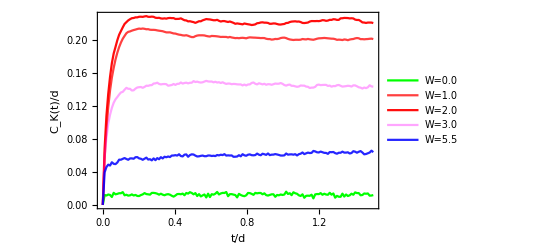

```mathematica
pKCNEEL1=Show[ListLinePlot[{Transpose[{tListN14,NeelKCW0}],Transpose[{tListN14,NeelKCW1}],Transpose[{tListN14,NeelKCW2}],Transpose[{tListN14,NeelKCW3}],Transpose[{tListN14,NeelKCW5pt5}]},PlotLegends->{"W=0.0","W=1.0","W=2.0","W=3.0","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[1,0,0,0.75],RGBColor[1,0,0,0.95],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/d",Bold,Black,14],Style["C_K(t)/d",Bold,Black,14]},LabelStyle->Directive[Bold,Black]]
```

```mathematica
Export["/Users/aneekphys/Documents/MBL1 plots/Neel_KC_L12.pdf",%]
```

/Users/aneekphys/Documents/MBL1 plots/Neel_KC_L12.pdf

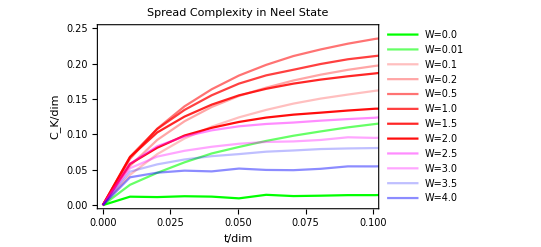

```mathematica
Show[ListLinePlot[{Transpose[{tListN14,NeelKCW0}],Transpose[{tListN14,NeelKCW0pt2}],Transpose[{tListN14,NeelKCW0pt5}],Transpose[{tListN14,NeelKCW1}],Transpose[{tListN14,NeelKCW1pt5}],Transpose[{tListN14,NeelKCW2}],Transpose[{tListN14,NeelKCW2pt5}],Transpose[{tListN14,NeelKCW3}],Transpose[{tListN14,NeelKCW3pt5}],Transpose[{tListN14,NeelKCW4}],Transpose[{tListN14,NeelKCW4pt5}],Transpose[{tListN14,NeelKCW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.0","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,0,0.85],RGBColor[1,0,0,0.95],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_K/dim",Bold,Black,16]},PlotLabel->Style["Spread Complexity in Neel State",Bold,Black],PlotRange->{{0,0.1},Automatic}]
```

```mathematica
NeelsatList = {NeelKCW0[[-100;;-1]]//Mean,NeelKCW0pt01[[-100;;-1]]//Mean,NeelKCW0pt1[[-100;;-1]]//Mean,NeelKCW0pt2[[-100;;-1]]//Mean,NeelKCW0pt5[[-100;;-1]]//Mean,NeelKCW1[[-100;;-1]]//Mean,NeelKCW1pt5[[-100;;-1]]//Mean,NeelKCW2[[-100;;-1]]//Mean,NeelKCW2pt5[[-100;;-1]]//Mean,NeelKCW3[[-100;;-1]]//Mean,NeelKCW3pt5[[-100;;-1]]//Mean,NeelKCW4[[-100;;-1]]//Mean,NeelKCW4pt5[[-100;;-1]]//Mean,NeelKCW5pt5[[-100;;-1]]//Mean};
wListN = {0,0.01,0.1,0.2,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5.5};
```

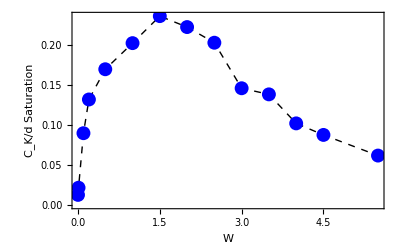

```mathematica
Show[ListLinePlot[Transpose[{wListN,NeelsatList}],PlotStyle->{Black,Dashed,Thick}],ListPlot[Transpose[{wListN,NeelsatList}],PlotStyle->{Blue,PointSize[0.025]}],Frame->True,FrameLabel->{Style["W",Bold,Black,14],Style["C_K/d Saturation",Bold,Black,14]},LabelStyle->Directive[Bold, Black,12]]
```

```mathematica
Export["/Users/aneekphys/Documents/MBL1 plots/KC_saturation_Neel_L12.pdf",%]
```

/Users/aneekphys/Documents/MBL1 plots/KC_saturation_Neel_L12.pdf

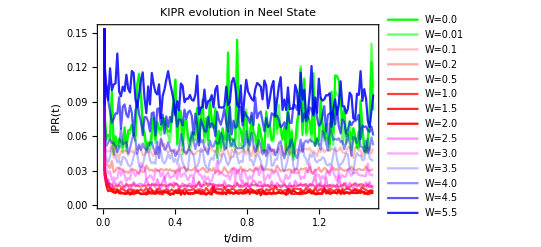

```mathematica
Show[ListLinePlot[{Transpose[{tListN14,NeelKIPRW0}],Transpose[{tListN14,NeelKIPRW0pt01}],Transpose[{tListN14,NeelKIPRW0pt1}],Transpose[{tListN14,NeelKIPRW0pt2}],Transpose[{tListN14,NeelKIPRW0pt5}],Transpose[{tListN14,NeelKIPRW1}],Transpose[{tListN14,NeelKIPRW1pt5}],Transpose[{tListN14,NeelKIPRW2}],Transpose[{tListN14,NeelKIPRW2pt5}],Transpose[{tListN14,NeelKIPRW3}],Transpose[{tListN14,NeelKIPRW3pt5}],Transpose[{tListN14,NeelKIPRW4}],Transpose[{tListN14,NeelKIPRW4pt5}],Transpose[{tListN14,NeelKIPRW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.0","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,0,0.85],RGBColor[1,0,0,0.95],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]},PlotRange->Automatic],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["KIPR evolution in Neel State",Bold,Black]]
```

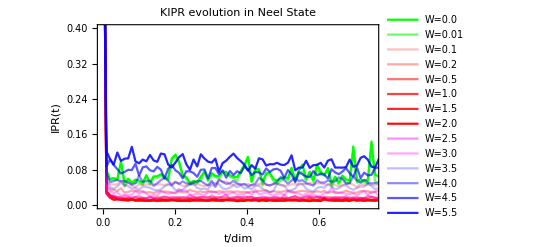

```mathematica
Show[ListLinePlot[{Transpose[{tListN14,NeelKIPRW0}],Transpose[{tListN14,NeelKIPRW0pt01}],Transpose[{tListN14,NeelKIPRW0pt1}],Transpose[{tListN14,NeelKIPRW0pt2}],Transpose[{tListN14,NeelKIPRW0pt5}],Transpose[{tListN14,NeelKIPRW1}],Transpose[{tListN14,NeelKIPRW1pt5}],Transpose[{tListN14,NeelKIPRW2}],Transpose[{tListN14,NeelKIPRW2pt5}],Transpose[{tListN14,NeelKIPRW3}],Transpose[{tListN14,NeelKIPRW3pt5}],Transpose[{tListN14,NeelKIPRW4}],Transpose[{tListN14,NeelKIPRW4pt5}],Transpose[{tListN14,NeelKIPRW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.0","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,0,0.85],RGBColor[1,0,0,0.95],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]},PlotRange->All],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["KIPR evolution in Neel State",Bold,Black],PlotRange->{{0,0.75},{0,0.4}}]
```

```mathematica
.
```

```mathematica
NeellIPRavSatList = {NeelKIPRW0[[-50;;-1]]//Mean,NeelKIPRW0pt01[[-50;;-1]]//Mean,NeelKIPRW0pt1[[-50;;-1]]//Mean,NeelKIPRW0pt2[[-50;;-1]]//Mean,NeelKIPRW0pt5[[-50;;-1]]//Mean,NeelKIPRW1[[-50;;-1]]//Mean,NeelKIPRW1pt5[[-50;;-1]]//Mean,NeelKIPRW2[[-50;;-1]]//Mean,NeelKIPRW2pt5[[-50;;-1]]//Mean,NeelKIPRW3[[-50;;-1]]//Mean,NeelKIPRW3pt5[[-50;;-1]]//Mean,NeelKIPRW4[[-50;;-1]]//Mean,NeelKIPRW4pt5[[-50;;-1]]//Mean,NeelKIPRW5pt5[[-50;;-1]]//Mean};
wListN = {0,0.01,0.1,0.2,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5.5};
```

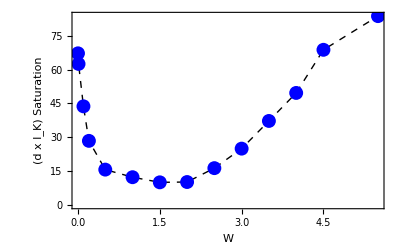

```mathematica
Show[ListLinePlot[Transpose[{wListN,924NeellIPRavSatList}],PlotStyle->{Black,Dashed,Thick}],ListPlot[Transpose[{wListN,924NeellIPRavSatList}],PlotStyle->{Blue,PointSize[0.025]}],Frame->True,FrameLabel->{Style["W",Bold,Black,14],Style["(d x I_K) Saturation",Bold,Black,14]},LabelStyle->Directive[Bold, Black,12]]
```

```mathematica
Export["/Users/aneekphys/Documents/MBL1 plots/KIPR_saturation_Neel_L12.pdf",%]
```

/Users/aneekphys/Documents/MBL1 plots/KIPR_saturation_Neel_L12.pdf

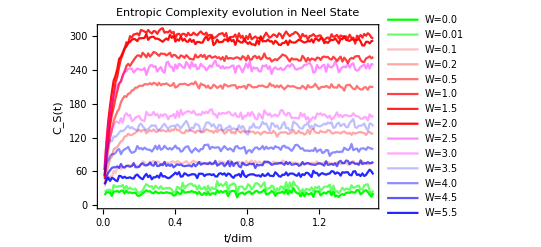

```mathematica
Show[ListLinePlot[{Transpose[{tListN14,NeelEntComplexityW0}],Transpose[{tListN14,NeelEntComplexityW0pt01}],Transpose[{tListN14,NeelEntComplexityW0pt1}],Transpose[{tListN14,NeelEntComplexityW0pt2}],Transpose[{tListN14,NeelEntComplexityW0pt5}],Transpose[{tListN14,NeelEntComplexityW1}],Transpose[{tListN14,NeelEntComplexityW1pt5}],Transpose[{tListN14,NeelEntComplexityW2}],Transpose[{tListN14,NeelEntComplexityW2pt5}],Transpose[{tListN14,NeelEntComplexityW3}],Transpose[{tListN14,NeelEntComplexityW3pt5}],Transpose[{tListN14,NeelEntComplexityW4}],Transpose[{tListN14,NeelEntComplexityW4pt5}],Transpose[{tListN14,NeelEntComplexityW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.0","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,0,0.85],RGBColor[1,0,0,0.95],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity evolution in Neel State",Bold,Black]]
```

```mathematica
NeellCsavSatList = {NeelEntComplexityW0[[-50;;-1]]//Mean,NeelEntComplexityW0pt01[[-50;;-1]]//Mean,NeelEntComplexityW0pt1[[-50;;-1]]//Mean,NeelEntComplexityW0pt2[[-50;;-1]]//Mean,NeelEntComplexityW0pt5[[-50;;-1]]//Mean,NeelEntComplexityW1[[-50;;-1]]//Mean,NeelEntComplexityW1pt5[[-50;;-1]]//Mean,NeelEntComplexityW2[[-50;;-1]]//Mean,NeelEntComplexityW2pt5[[-50;;-1]]//Mean,NeelEntComplexityW3[[-50;;-1]]//Mean,NeelEntComplexityW3pt5[[-50;;-1]]//Mean,NeelEntComplexityW4[[-50;;-1]]//Mean,NeelEntComplexityW4pt5[[-50;;-1]]//Mean,NeelEntComplexityW5pt5[[-50;;-1]]//Mean};
wListN = {0,0.01,0.1,0.2,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5.5};
```

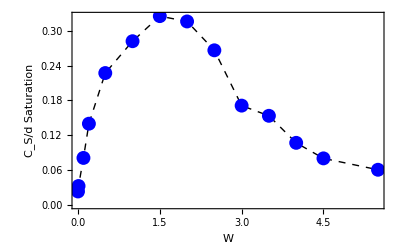

```mathematica
Show[ListLinePlot[Transpose[{wListN,NeellCsavSatList/924}],PlotStyle->{Black,Dashed,Thick}],ListPlot[Transpose[{wListN,NeellCsavSatList/924}],PlotStyle->{Blue,PointSize[0.025]}],Frame->True,FrameLabel->{Style["W",Bold,Black,14],Style["C_S/d Saturation",Bold,Black,14]},LabelStyle->Directive[Bold, Black,12]]
```

```mathematica
Export["/Users/aneekphys/Documents/MBL1 plots/KEC_saturation_Neel_L12.pdf",%]
```

/Users/aneekphys/Documents/MBL1 plots/KEC_saturation_Neel_L12.pdf

```mathematica
?PlotStyle
```